```mathematica
SetDirectory[NotebookDirectory[]];
```

## 5

```mathematica
data=Sort[{57,61,46,43,46,46,46,46,55}]
```

{43,46,46,46,46,46,55,57,61}

```mathematica
|
```

```mathematica
Variance@data
```

725/18

```mathematica
N[725/18]
```

40.2778

```mathematica
Mean@%
```

446/9

```mathematica
N[446/9]
```

49.5556

```mathematica
StandardDeviation@data
```

(5 √(29/2))/3

```mathematica
N[(5 √(29/2))/3]
```

6.34648

```mathematica
Sqrt[40.3]
```

6.34823

```mathematica
olinfaculty={63,66,71,65,70,66,67,65,67,74,64,75,68,67,70,73,66,70,72,62,68,70,62,69,66,70,70,68,69,70,71,65,64,71,64,78,69,70,65,66,72,64};
```

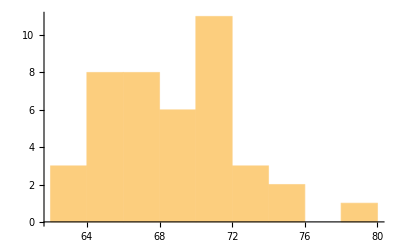
-Graphics-
(Mean[olinfaculty]==477/7)≈68.1429
(Total[olinfaculty]/Length[olinfaculty]==477/7)≈68.1429
(StandardDeviation[olinfaculty]==√(3662/287))≈3.57206
(√(Total[(olinfaculty-Mean[olinfaculty])^2]/(Length[olinfaculty]-1))==√(3662/287))≈3.57206

table1.png

```mathematica
Grid[{{Histogram[olinfaculty,6]},
{TraditionalForm[HoldForm[Mean[olinfaculty]]==Mean[olinfaculty]≈N@Mean[olinfaculty]]},
{TraditionalForm[HoldForm[Total[olinfaculty]/Length[olinfaculty]]==Total[olinfaculty]/Length[olinfaculty]≈N@Mean[olinfaculty]]},
{TraditionalForm[HoldForm[StandardDeviation[olinfaculty]]==StandardDeviation[olinfaculty]≈N@StandardDeviation[olinfaculty]]},
{TraditionalForm[HoldForm[Sqrt[Total[(olinfaculty-Mean[olinfaculty])^2]/(Length@olinfaculty-1)]]==Sqrt[Total[(olinfaculty-Mean[olinfaculty])^2]/(Length@olinfaculty-1)]≈N@Sqrt[Total[(olinfaculty-Mean[olinfaculty])^2]/(Length@olinfaculty-1)]]}},Frame->All]
Export["table1.png",%]
```

## 6: States

```mathematica
statedata=Import["stateData.csv"][[2;;All]];
university=statedata[[All,8]];
mortality=statedata[[All,3]];
income=statedata[[All,10]];
unemployment=statedata[[All,7]];
```

```mathematica
normalize[vec_]:=(vec-Mean[vec])/StandardDeviation[vec]
```

```mathematica
normalized=normalize/@{university,income,mortality};
```

```mathematica
Labeled[ Grid[Prepend[N@Transpose[normalized],StringSplit["University Income Mortality"]],Frame->All],"Normalized vectors"]
Export["Normalized vectors.png",%]
```

University | Income | Mortality
-1.08552 | -1.21398 | 1.57928
-0.00509633 | 1.34336 | -0.0652596
-0.453573 | -0.391869 | -0.456817
-1.73785 | -1.59578 | 1.18772
0.463766 | 0.605823 | -1.55318
1.68688 | 0.206469 | -1.005
1.68688 | 1.35674 | -0.61344
0.0356743 | 0.305217 | 1.0311
-0.310876 | -0.707149 | 0.247986
0.0356743 | -0.401486 | 0.874478
0.361839 | 1.21983 | -1.08331
-0.677812 | -0.727176 | -0.143571Normalized vectors

Normalized vectors.png

```mathematica
normalized.Transpose@normalized / (Length@income-1)//MatrixForm
```

(1. | 0.757318 | -0.665918
0.757318 | 1. | -0.648249
-0.665918 | -0.648249 | 1.)

## 10: equations

```mathematica
y[x_]:=a x+b
Solve[{y[60]==22,y[300]==24},{a,b}]
```

{{a→1/120,b→43/2}}

## 11: Matrix equations

```mathematica
eqn=({{60, 1}, {300, 1}}).({{a}, {b}})==({{22}, {24}});
Solve[eqn,Variables@eqn]
```

{{a→1/120,b→43/2}}

```mathematica
data=({{60, 1}, {300, 1}});
Inverse[data]//MatrixForm
%.({{22}, {24}})//MatrixForm
```

(-1/240 | 1/240
5/4 | -1/4)

(1/120
43/2)

```mathematica
HoldForm[({{60, 1}, {300, 1}}).({{a}, {b}})]==({{60, 1}, {300, 1}}).({{a}, {b}})//TraditionalForm
```

(60 | 1
300 | 1).(a
b)==(60 a+b
300 a+b)

## 13-14: Crickets

```mathematica
t={53,54,58,66,69,70,71,73,81};
c={19,26,21,33,31,36,36,38,45};
```

```mathematica
sums=Total /@ {c,t,c^2,c t}
```

{285,595,9589,19441}

```mathematica
Clear[a,b]
eqs={a sums[[3]]+b sums[[1]]==sums[[4]],Length@t b + a sums[[1]]==sums[[2]]}//TraditionalForm
```

{9589 a+285 b==19441,285 a+9 b==595}

```mathematica
mateqn=({{9589, 285}, {285, 9}}).({{a}, {b}})==({{19441}, {595}});
mateqn//TraditionalForm
```

(9589 a+285 b
285 a+9 b)==(19441
595)

```mathematica
Reduce[{{9589 a+285 b},{285 a+9 b}}=={{19441},{595}}]
N@%
```

b==82385/2538&&a==899/846

b==32.4606&&a==1.06265

{{a→899/846,b→82385/2538}}

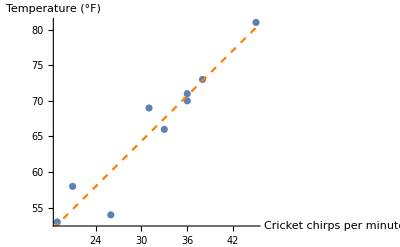

Crickets.png

```mathematica
sol=Solve[mateqn,Variables@mateqn]
Show[ListPlot[Transpose[{c,t}],AxesLabel->{"Cricket chirps per minute","Temperature (°F)"}],Plot[a x+b/.sol,{x,0,100},PlotStyle->{Orange,Dashed}]]
Export["Crickets.png",Rasterize[%,RasterSize->1000,ImageSize->Large]]
```